```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

```mathematica
phiBar[deltaPhi_,T_]:=deltaPhi/T;
```

```mathematica
phiBarK[phiBar_,κ_]:=phiBar/(1-3/(2 κ));
```

```mathematica
Cp6:=phiBar^(3/2)/(√π(1-3/(2 κ))^(3/2))Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

```mathematica
Cp6Func[κ_]:=phiBar^(3/2)/(√π(1-3/(2 κ))^(3/2))Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

## Plot integrand √(Ē+1)(1+(Ē ϕ̄)/(κ-3/2))^(-(κ+1))

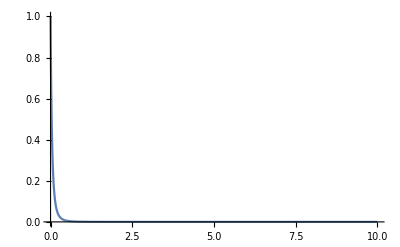

```mathematica
Plot[√(Ebar+1)(1+ (Ebar #2)/(#1- 3/2))^(-(#1+1)),{Ebar,0,10},PlotRange->Full]&[3,941/110]
```

## Try series expansions of Energy Integral 1 integrand (didn’t work) (Use a = (ϕ̄)/(κ-3/2))

```mathematica
this=Series[√(1+x)(1+ a x)^(-(κ+1)),{x,0,10},Assumptions->κ>3/2]
```

1+(1/2-a (1+κ)) x+(-1/8-1/2 a (1+κ)+1/2 a^2 (1+κ) (2+κ)) x^2+(1/16+1/8 a (1+κ)+1/4 a^2 (1+κ) (2+κ)-1/6 a^3 (1+κ) (2+κ) (3+κ)) x^3+(-5/128+1/24 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)-1/16 a (1+κ)-1/16 a^2 (1+κ) (2+κ)-1/12 a^3 (1+κ) (2+κ) (3+κ)) x^4+(7/256+1/48 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)+1/120 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)+5/128 a (1+κ)+1/32 a^2 (1+κ) (2+κ)+1/48 a^3 (1+κ) (2+κ) (3+κ)) x^5+(-21/1024-1/192 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)+1/240 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)+1/720 a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)-7/256 a (1+κ)-5/256 a^2 (1+κ) (2+κ)-1/96 a^3 (1+κ) (2+κ) (3+κ)) x^6+(33/2048+1/384 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)-1/960 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)+(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/1440+(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/5040+(21 a (1+κ))/1024+7/512 a^2 (1+κ) (2+κ)+5/768 a^3 (1+κ) (2+κ) (3+κ)) x^7+(-429/32768-(5 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ))/3072+(a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/1920-(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/5760+(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/10080+(a^8 (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/40320-(33 a (1+κ))/2048-(21 a^2 (1+κ) (2+κ))/2048-(7 a^3 (1+κ) (2+κ) (3+κ))/1536) x^8+(715/65536+(7 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ))/6144-(a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/3072+(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/11520-(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/40320+(a^8 (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/80640+(a^9 (-9-κ) (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/362880+(429 a (1+κ))/32768+(33 a^2 (1+κ) (2+κ))/4096+(7 a^3 (1+κ) (2+κ) (3+κ))/2048) x^9+(-2431/262144-(7 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ))/8192+(7 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/30720-(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/18432+(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/80640-(a^8 (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/322560+(a^9 (-9-κ) (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/725760+(a^10 (-10-κ) (-9-κ) (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/3628800-(715 a (1+κ))/65536-(429 a^2 (1+κ) (2+κ))/65536-(11 a^3 (1+κ) (2+κ) (3+κ))/4096) x^10+O[x]^11

```mathematica
CoefficientList[this,x]
```

{1,1/2-a (1+κ),-1/8-1/2 a (1+κ)+1/2 a^2 (1+κ) (2+κ),1/16+1/8 a (1+κ)+1/4 a^2 (1+κ) (2+κ)-1/6 a^3 (1+κ) (2+κ) (3+κ),-5/128+1/24 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)-1/16 a (1+κ)-1/16 a^2 (1+κ) (2+κ)-1/12 a^3 (1+κ) (2+κ) (3+κ),7/256+1/48 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)+1/120 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)+5/128 a (1+κ)+1/32 a^2 (1+κ) (2+κ)+1/48 a^3 (1+κ) (2+κ) (3+κ),-21/1024-1/192 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)+1/240 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)+1/720 a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)-7/256 a (1+κ)-5/256 a^2 (1+κ) (2+κ)-1/96 a^3 (1+κ) (2+κ) (3+κ),33/2048+1/384 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ)-1/960 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ)+(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/1440+(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/5040+(21 a (1+κ))/1024+7/512 a^2 (1+κ) (2+κ)+5/768 a^3 (1+κ) (2+κ) (3+κ),-429/32768-(5 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ))/3072+(a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/1920-(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/5760+(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/10080+(a^8 (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/40320-(33 a (1+κ))/2048-(21 a^2 (1+κ) (2+κ))/2048-(7 a^3 (1+κ) (2+κ) (3+κ))/1536,715/65536+(7 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ))/6144-(a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/3072+(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/11520-(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/40320+(a^8 (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/80640+(a^9 (-9-κ) (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/362880+(429 a (1+κ))/32768+(33 a^2 (1+κ) (2+κ))/4096+(7 a^3 (1+κ) (2+κ) (3+κ))/2048,-2431/262144-(7 a^4 (-4-κ) (-3-κ) (-2-κ) (-1-κ))/8192+(7 a^5 (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/30720-(a^6 (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/18432+(a^7 (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/80640-(a^8 (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/322560+(a^9 (-9-κ) (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/725760+(a^10 (-10-κ) (-9-κ) (-8-κ) (-7-κ) (-6-κ) (-5-κ) (-4-κ) (-3-κ) (-2-κ) (-1-κ))/3628800-(715 a (1+κ))/65536-(429 a^2 (1+κ) (2+κ))/65536-(11 a^3 (1+κ) (2+κ) (3+κ))/4096}

## Try energy integral 1 with various integer values of κ

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ - 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->Element[κ,Integers]&&phiBar>0]
```

#### κ=2

```mathematica
IE1= Integrate[√(Ebar+1)(1+ 2 Ebar phiBar)^-3,{Ebar,0,∞},Assumptions->phiBar>0]
```

(-16 √(1-2 phiBar) phiBar^(3/2)+4 √(phiBar-2 phiBar^2)+√2 π-2 √2 ArcSin[√2 √phiBar])/(32 ((1-2 phiBar) phiBar)^(3/2))

#### κ=3

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(# - 3/2))^(-(#+1)),{Ebar,0,∞},Assumptions->Element[κ,Integers]&&phiBar>0]&[3]
```

(-336+108/phiBar+128 phiBar+(81 π)/(√(3/2-phiBar) phiBar^(3/2))-(162 ArcSin[√(2/3) √phiBar])/(√(3/2-phiBar) phiBar^(3/2)))/(64 (3-2 phiBar)^2)

#### κ=4

```mathematica
IE1= Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(# - 3/2))^(-(#+1)),{Ebar,0,∞},Assumptions->Element[κ,Integers]&&phiBar>0]&[4]
```

-1/(1536 (5-2 phiBar)^(7/2) phiBar^(3/2))5 (23600 √(5-2 phiBar) phiBar^(3/2)-10880 √(5-2 phiBar) phiBar^(5/2)+1536 √(5-2 phiBar) phiBar^(7/2)-7500 √((5-2 phiBar) phiBar)-9375 √2 π+18750 √2 ArcSin[√(2/5) √phiBar])

```mathematica
FullSimplify[%]
```

(5 (11800-3750/phiBar-5440 phiBar+768 phiBar^2-(9375 ArcCos[√(2/5) √phiBar])/(√(5/2-phiBar) phiBar^(3/2))))/(768 (-5+2 phiBar)^3)

## Integrals performed for κ=2–5

```mathematica
(*Keq2[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[2]*)
```

```mathematica
(*Keq3[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[3]*)
```

```mathematica
(*Keq4[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[4]*)
```

```mathematica
(*Keq5[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[5]*)
```

## Analytic expressions for κ=2–5

```mathematica
Keq2[phiBar_,RB_]:=((4 phiBar^2 RB)/((-1+2 phiBar) (-1+2 phiBar+RB))+(√2 √phiBar ArcCos[√2 √phiBar])/(1-2 phiBar)^(3/2)+(√2 √phiBar √(1+(2 phiBar)/(-1+RB)) (-1+RB)^(5/2) ArcSinh[(√2 √phiBar)/(√(-1+RB))])/(-1+2 phiBar+RB)^2)/(√2 √phiBar π)
```

```mathematica
Keq3[phiBar_,RB_]:=((4 √2 phiBar^(3/2) (4 phiBar^2+15 phiBar (-2+RB)-36 (-1+RB)) RB)/((3-2 phiBar)^2 (-3+2 phiBar+3 RB)^2)+(27 ArcCos[√(2/3) √phiBar])/(3-2 phiBar)^(5/2)+(27 √(-1+RB) ArcSinh[(√(2/3) √phiBar)/(√(-1+RB))])/(3+(2 phiBar)/(-1+RB))^(5/2))/(√3 π)
```

```mathematica
Keq4[phiBar_,RB_]:=1/(30 √10 π)(8 phiBar^(3/2) ((1825+2 phiBar (-455+66 phiBar))/(-5+2 phiBar)^3-(60 phiBar^2)/(-5+2 phiBar+5 RB)^3+(110 phiBar)/(-5+2 phiBar+5 RB)^2-73/(-5+2 phiBar+5 RB))+(18750 √2 ArcCos[√(2/5) √phiBar])/(5-2 phiBar)^(7/2)+(18750 √(10+(4 phiBar)/(-1+RB)) (-1+RB)^(9/2) ArcSinh[(√(2/5) √phiBar)/(√(-1+RB))])/(-5+2 phiBar+5 RB)^4)
```

```mathematica
Keq5[phiBar_,RB_]:=1/(210 √14 π)(16 phiBar^(3/2) ((-135485+2 phiBar (36113+6 phiBar (-1246+93 phiBar)))/(7-2 phiBar)^4+(420 phiBar^3)/(-7+2 phiBar+7 RB)^4-(980 phiBar^2)/(-7+2 phiBar+7 RB)^3+(896 phiBar)/(-7+2 phiBar+7 RB)^2-395/(-7+2 phiBar+7 RB))-(3529470 √(14-4 phiBar) ArcCos[√(2/7) √phiBar])/(-7+2 phiBar)^5+(3529470 √(14+(4 phiBar)/(-1+RB)) (-1+RB)^(11/2) ArcSinh[(√(2/7) √phiBar)/(√(-1+RB))])/(-7+2 phiBar+7 RB)^5)
```

```mathematica
Keq6[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[6]
```

```mathematica
Keq7[phiBar_,RB_]=FullSimplify[Cp6Func[#]*(IE1Func[#]-1/(RB-1)IE2Func[#])/.phiBarOverRBm1->phiBar/(RB-1)]&[7]
```

## Plots for various integer κ

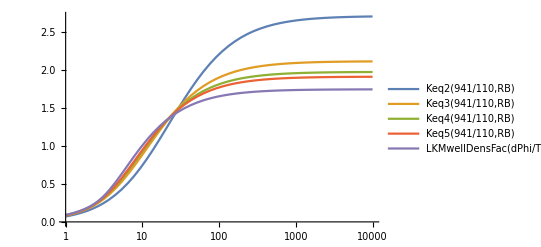

```mathematica
LogLinearPlot[{Keq2[941/110,RB],Keq3[941/110,RB],Keq4[941/110,RB],Keq5[941/110,RB],LKMwellDensFac[dPhi/Tm,RB]},{RB,1,10000},PlotLegends->"Expressions"]
```

```mathematica
Clear[Keq2]
```

## Outrightly obtain expression for non-integer κ (uses ϕ̄= (e Δ Φ)/T, not (ϕ̄)_κ!)

```mathematica
IE1Norm=Cp6  Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ - 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->κ≥ 3/2&&phiBar>0]
```

-1/(2 √π (1-3/(2 κ))^(3/2) κ^(3/2) Gamma[-1/2+κ])√phiBar (-(12+8 phiBar-8 κ)^-κ √((6+4 phiBar-4 κ)/phiBar) (-3+2 κ)^(1+κ) Gamma[1-κ] Gamma[-1+2 κ]+(3 Gamma[κ]-2 Gamma[1+κ]) Hypergeometric2F1[-1/2,1,1-κ,(-3+2 κ)/(2 phiBar)])

```mathematica
Gamma[-3]
```

ComplexInfinity

```mathematica
IE2Norm=Cp6 Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarOverRBm1>0]/.phiBarOverRBm1->phiBar/(RB-1)
```

((-1+RB)^2 Gamma[1+κ] ((-(3-2 κ)^2+(8 phiBar^2 κ)/(-1+RB)^2+(2 phiBar (3-8 κ+4 κ^2))/(-1+RB)) Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))]+((3-2 κ)^2-(4 phiBar^2 (-1+6 κ+4 κ^2))/(-1+RB)^2+(phiBar (-30+8 κ+8 κ^2))/(-1+RB)) Hypergeometric2F1[1,1+κ,1/2,(2 phiBar)/((-1+RB) (3-2 κ))]))/(2 √phiBar √π (1-3/(2 κ))^(3/2) κ^(3/2) (-1+4 κ^2) Gamma[-1/2+κ])

```mathematica
IE2Full=-Cp6/(RB-1) Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarOverRBm1>0]/.phiBarOverRBm1->phiBar/(RB-1)
```

-(((-1+RB) Gamma[1+κ] ((-3+(2 phiBar)/(-1+RB)+2 κ) (3+(-2+(4 phiBar)/(-1+RB)) κ) Hypergeometric2F1[1,1+κ,-1/2,(2 phiBar)/((-1+RB) (3-2 κ))]+((3-2 κ)^2-(4 phiBar^2 (-1+6 κ+4 κ^2))/(-1+RB)^2+(phiBar (-30+8 κ (1+κ)))/(-1+RB)) Hypergeometric2F1[1,1+κ,1/2,(2 phiBar)/((-1+RB) (3-2 κ))]))/(2 √phiBar √π (1-3/(2 κ))^(3/2) κ^(3/2) (-1+4 κ^2) Gamma[-1/2+κ]))

```mathematica
IE2Full=-Cp6/(RB-1) Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarOverRBm1>0]
```

-((phiBar^(3/2) Gamma[1+κ] ((-3+2 phiBarOverRBm1+2 κ) (3+(-2+4 phiBarOverRBm1) κ) Hypergeometric2F1[1,1+κ,-1/2,(2 phiBarOverRBm1)/(3-2 κ)]+((3-2 κ)^2-4 phiBarOverRBm1^2 (-1+6 κ+4 κ^2)+phiBarOverRBm1 (-30+8 κ (1+κ))) Hypergeometric2F1[1,1+κ,1/2,(2 phiBarOverRBm1)/(3-2 κ)]))/(2 phiBarOverRBm1^2 √π (-1+RB) (1-3/(2 κ))^(3/2) κ^(3/2) (-1+4 κ^2) Gamma[-1/2+κ]))

```mathematica
IE1Func[κ_]:=Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ- 3/2))^(-(κ+1)),{Ebar,0,∞},Assumptions->phiBar>0]
```

```mathematica
IE2Func[κ_]:=Integrate[√(1-Ebar)(1+ (Ebar phiBarOverRBm1)/(κ - 3/2))^(-(κ+1)),{Ebar,0,1},Assumptions->phiBarOverRBm1>0]
```

```mathematica
Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(2- 3/2))^(-(2+1)),Ebar,Assumptions->phiBar>0]
```

(√(1+Ebar) (1-2 (2+Ebar) phiBar))/(8 phiBar (-1+2 phiBar) (1+2 Ebar phiBar)^2)+ArcTan[(√2 √(1+Ebar) √phiBar)/(√(1-2 phiBar))]/(8 √2 (1-2 phiBar)^(3/2) phiBar^(3/2))

```mathematica
Integrate[√(Ebar+1)(1+ (Ebar phiBar)/(κ- 3/2))^(-(κ+1)),Ebar,Assumptions->phiBar>0]
```

-(2 (1+Ebar)^(3/2) ((3-2 Ebar phiBar-2 κ)/(3+2 phiBar-2 κ))^κ (-3+2 κ) ((-3+2 Ebar phiBar+2 κ)/(-3+2 κ))^-κ Hypergeometric2F1[3/2,1+κ,5/2,(2 (1+Ebar) phiBar)/(3+2 phiBar-2 κ)])/(3 (3+2 phiBar-2 κ))

```mathematica
Limit[-(2 (1+Ebar)^(3/2) ((3-2 Ebar phiBar-2 κ)/(3+2 phiBar-2 κ))^κ (-3+2 κ) ((-3+2 Ebar phiBar+2 κ)/(-3+2 κ))^-κ Hypergeometric2F1[3/2,1+κ,5/2,(2 (1+Ebar) phiBar)/(3+2 phiBar-2 κ)])/(3 (3+2 phiBar-2 κ)),Ebar->∞]
```

## Outrightly obtain expressions for non-integer κ (uses (ϕ̄)_κ≡(e ΔΦ)/(T (1-3/(2 κ))))

```mathematica
Cp6:=phiBarK^(3/2)/(√π)Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

```mathematica
IE1Norm=Integrate[√(Ebar+1)(1+ (Ebar phiBarK)/κ)^(-(κ+1)),{Ebar,0,∞},Assumptions->κ≥ 3/2&&phiBarK>0]
```

((phiBarK-κ)^(1/2-κ) κ^κ Gamma[1-κ] Gamma[-1/2+κ])/(2 phiBarK^(3/2) √π)+Hypergeometric2F1[-1/2,1,1-κ,κ/phiBarK]/phiBarK

```mathematica
FullSimplify[IE1Norm]
```

((phiBarK-κ)^(1/2-κ) κ^κ Gamma[1-κ] Gamma[-1/2+κ])/(2 phiBarK^(3/2) √π)+Hypergeometric2F1[-1/2,1,1-κ,κ/phiBarK]/phiBarK

```mathematica
IE2Full=-1/(RB-1) Integrate[√(1-Ebar)(1+ (Ebar phiBarKOverRBm1)/κ)^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarKOverRBm1>0]/.phiBarKOverRBm1->phiBarK/(RB-1)
```

-1/(phiBarK^2 (-1+4 κ^2))2 (-1+RB) ((-1+(2 phiBarK)/(-1+RB)) κ (phiBarK/(-1+RB)+κ) Hypergeometric2F1[1,1+κ,-1/2,-phiBarK/((-1+RB) κ)]+(κ^2+(phiBarK κ (5+2 κ))/(-1+RB)+(phiBarK^2 (1-2 κ (3+2 κ)))/(-1+RB)^2) Hypergeometric2F1[1,1+κ,1/2,-phiBarK/((-1+RB) κ)])

```mathematica
FullSimplify[Cp6(IE1Norm+IE2Full)]
```

1/4 (2 (phiBarK-κ)^(1/2-κ) κ^(-1/2+κ) Csc[π κ]+1/(phiBarK^(3/2) √π √κ)(1/((-1+RB) Gamma[5/2+κ])Gamma[κ] ((-1+RB) κ ((-1+RB)^2 κ^2+phiBarK (-1+RB) κ (5+2 κ)+phiBarK^2 (1-2 κ (3+2 κ)))-(phiBarK+(-1+RB) κ)^3 Hypergeometric2F1[1,1+κ,-1/2,phiBarK/(κ-RB κ)])+(4 phiBarK^2 π Csc[π κ] Hypergeometric2F1Regularized[-1/2,1,1-κ,κ/phiBarK])/Gamma[-1/2+κ]))

```mathematica
densFacK[phiBarK_,RB_,κ_]:=1/4( 2 (phiBarK-κ)^(1/2-κ) κ^(-1/2+κ) Csc[π κ]+1/(phiBarK^(3/2) √π √κ)(Gamma[κ]/((-1+RB) Gamma[5/2+κ]) ((-1+RB) κ ((-1+RB)^2 κ^2+phiBarK (-1+RB) κ (5+2 κ)+phiBarK^2 (1-2 κ (3+2 κ)))-(phiBarK+(-1+RB) κ)^3 Hypergeometric2F1[1,1+κ,-1/2,phiBarK/(κ-RB κ)])+(4 phiBarK^2 π Csc[π κ] Hypergeometric2F1Regularized[-1/2,1,1-κ,κ/phiBarK])/Gamma[-1/2+κ]));
```

## Plot comparing analytic kappa curve and analytic Maxwellian curve (but integer kappa is still no dice!)

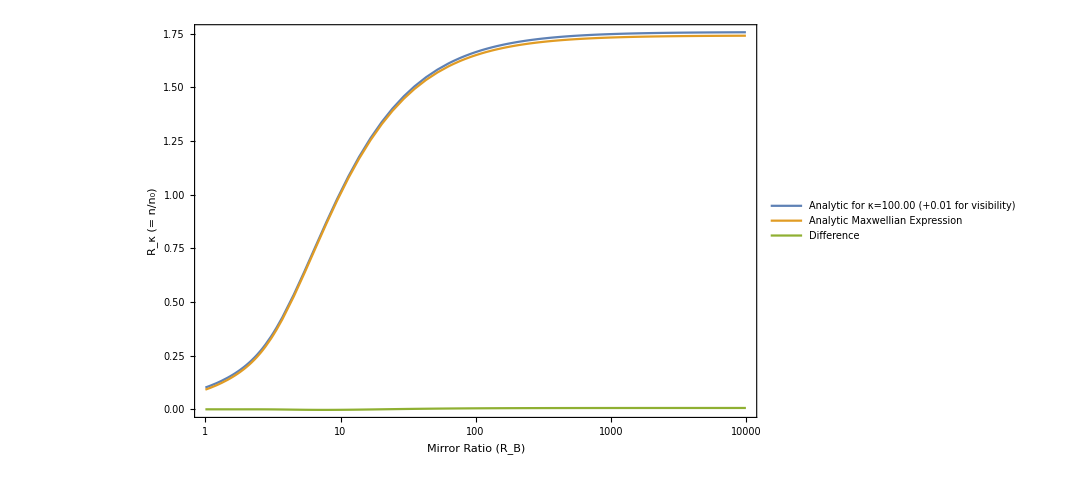

```mathematica
LogLinearPlot[{Abs[densFacK[phiBarK[941/110,#],RB,#]]+0.01,LKMwellDensFac[941/110,RB],Abs[densFacK[phiBarK[941/110,#],RB,#]]-LKMwellDensFac[941/110,RB]},{RB,1,10000},PlotLegends->{StringForm["Analytic for κ=`1` (+0.01 for visibility)",NumberForm[N[#],{3,2}]],"Analytic Maxwellian Expression","Difference"},Frame->True,FrameLabel->{"Mirror Ratio (R_B)","R_κ (= n/n_0)"},FrameStyle->(FontSize->18),ImageSize->800]&[1001/10]
```

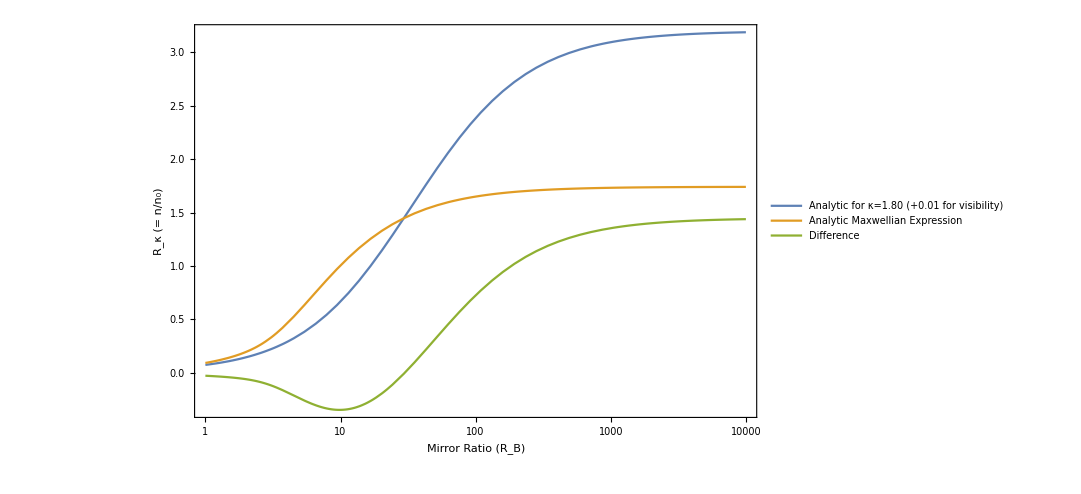

```mathematica
LogLinearPlot[{Abs[densFacK[phiBarK[941/110,#],RB,#]]+0.01,LKMwellDensFac[941/110,RB],Abs[densFacK[phiBarK[941/110,#],RB,#]]-LKMwellDensFac[941/110,RB]},{RB,1,10000},PlotLegends->{StringForm["Analytic for κ=`1` (+0.01 for visibility)",NumberForm[N[#],{3,2}]],"Analytic Maxwellian Expression","Difference"},Frame->True,FrameLabel->{"Mirror Ratio (R_B)","R_κ (= n/n_0)"},FrameStyle->(FontSize->18),ImageSize->800]&[18/10]
```

```mathematica
IE2Full=-Cp6/(RB-1) Integrate[√(1-Ebar)(1+ (Ebar phiBarKOverRBm1)/κ)^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarKOverRBm1>0]
```

```mathematica
IE1Func[κ_]:=Integrate[√(Ebar+1)(1+ (Ebar phiBarK)/κ)^(-(κ+1)),{Ebar,0,∞},Assumptions->phiBarK>0]
```

```mathematica
IE2Func[κ_]:=Integrate[√(1-Ebar)(1+ (Ebar phiBarKOverRBm1)/κ)^(-(κ+1)),{Ebar,0,1},Assumptions->phiBarKOverRBm1>0]
```

## 2018/02/09 Compare specific terms in Maxwellian n/n_0=1/2 e^(ϕ̄)erfc √(ϕ̄)+√((R_B-1)/π)D √((ϕ̄)/(R_B-1))with kappa expression

## Mess with Γ(w)Γ(z)=((w+z-2)!)/(_(z-1)^(w+z-2))

```mathematica
z=1-κ;w=2 κ - 1;
```

```mathematica
z+w-2
```

-2+κ

```mathematica
z=2κ-1
```

-1+2 κ

```mathematica
n-z/.n->κ
```

1-κ

```mathematica
Gamma[w]Gamma[z]
```

Gamma[1-κ] Gamma[-1+2 κ]

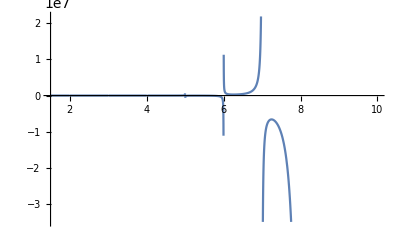

```mathematica
Plot[{Gamma[w]Gamma[z]},{κ,3/2,10}]
```

```mathematica
Plot[{(w+z-2)!/Binomial[w+z-2,z-1]},{κ,3/2,10}]
```

-Graphics-

## Outrightly obtain expressions for integer κ (uses (ϕ̄)_κ≡(e ΔΦ)/(T (1-3/(2 κ))))

```mathematica
Cp6:=phiBarK^(3/2)/(√π)Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])
```

```mathematica
IE1Norm=Limit[Integrate[√(Ebar+1)(1+ (Ebar phiBarK)/κ)^(-(κ+1)),{Ebar,0,∞},Assumptions->{κ∈Integers&&κ>3/2&&phiBarK>0}],κ->1]
```

$Aborted

```mathematica
Series[√(Ebar+1)(1+ a Ebar)^(-(κ+1)),{Ebar,0,5}]
```

1+(1/2-a (1+κ)) Ebar+(-1/8-1/2 a (1+κ)+1/2 a^2 (1+κ) (2+κ)) Ebar^2+(1/16+1/8 a (1+κ)+1/4 a^2 (1+κ) (2+κ)-1/6 a^3 (1+κ) (2+κ) (3+κ)) Ebar^3+(-5/128-1/16 a (1+κ)-1/16 a^2 (1+κ) (2+κ)-1/12 a^3 (1+κ) (2+κ) (3+κ)+1/24 a^4 (1+κ) (2+κ) (3+κ) (4+κ)) Ebar^4+(7/256+5/128 a (1+κ)+1/32 a^2 (1+κ) (2+κ)+1/48 a^3 (1+κ) (2+κ) (3+κ)+1/48 a^4 (1+κ) (2+κ) (3+κ) (4+κ)-1/120 a^5 (1+κ) (2+κ) (3+κ) (4+κ) (5+κ)) Ebar^5+O[Ebar]^6

```mathematica
CoefficientList[%164,Ebar]
```

{1,1/2-a (1+κ),-1/8-1/2 a (1+κ)+1/2 a^2 (1+κ) (2+κ),1/16+1/8 a (1+κ)+1/4 a^2 (1+κ) (2+κ)-1/6 a^3 (1+κ) (2+κ) (3+κ),-5/128-1/16 a (1+κ)-1/16 a^2 (1+κ) (2+κ)-1/12 a^3 (1+κ) (2+κ) (3+κ)+1/24 a^4 (1+κ) (2+κ) (3+κ) (4+κ),7/256+5/128 a (1+κ)+1/32 a^2 (1+κ) (2+κ)+1/48 a^3 (1+κ) (2+κ) (3+κ)+1/48 a^4 (1+κ) (2+κ) (3+κ) (4+κ)-1/120 a^5 (1+κ) (2+κ) (3+κ) (4+κ) (5+κ)}

```mathematica
Simplify[((phiBarK-κ)^(1/2-κ) κ^κ Gamma[1-κ] Gamma[-1/2+κ])/(2 phiBarK^(3/2) √π)+Hypergeometric2F1[-1/2,1,1-κ,κ/phiBarK]/phiBarK,κ∈Integers&&κ>0]
```

Simplify::infd: Expression Gamma[1-κ] simplified to ComplexInfinity.

Simplify::infd: Expression √(phiBarK-κ) κ^κ Gamma[1-κ] Gamma[-1/2+κ] simplified to ComplexInfinity.

Simplify::infd: Expression √(phiBarK-κ) κ^κ Gamma[1-κ] Gamma[-1/2+κ]+2 √phiBarK √π (phiBarK-κ)^κ Hypergeometric2F1[-1/2,1,1-κ,κ/phiBarK] simplified to ComplexInfinity.

General::stop: Further output of Simplify::infd will be suppressed during this calculation.

ComplexInfinity

```mathematica
FullSimplify[IE1Norm]
```

((phiBarK-κ)^(1/2-κ) κ^κ Gamma[1-κ] Gamma[-1/2+κ])/(2 phiBarK^(3/2) √π)+Hypergeometric2F1[-1/2,1,1-κ,κ/phiBarK]/phiBarK

```mathematica
IE2Full=-1/(RB-1) Integrate[√(1-Ebar)(1+ (Ebar phiBarKOverRBm1)/κ)^(-(κ+1)),{Ebar,0,1},Assumptions->κ>3/2&&phiBarKOverRBm1>0]/.phiBarKOverRBm1->phiBarK/(RB-1)
```

-1/(phiBarK^2 (-1+4 κ^2))2 (-1+RB) ((-1+(2 phiBarK)/(-1+RB)) κ (phiBarK/(-1+RB)+κ) Hypergeometric2F1[1,1+κ,-1/2,-phiBarK/((-1+RB) κ)]+(κ^2+(phiBarK κ (5+2 κ))/(-1+RB)+(phiBarK^2 (1-2 κ (3+2 κ)))/(-1+RB)^2) Hypergeometric2F1[1,1+κ,1/2,-phiBarK/((-1+RB) κ)])